## Riemann–Stieltjes Integrals

```mathematica
Clear[f,g]
f[s_]:=s^3-2 s^2+3/2s+1/8
g[s_]:=Sin[2π s]
n=15;
t = Range[0,n]/n;
dg = N@Differences[g[t]];
integral =Total[dg*f[Drop[t,-1]]]
```

-0.188185

```mathematica
(*Clear[f,g]
f[x_]:=Exp[x]
n=50;
t = Range[0,n]/n;
g=ListInterpolation[First[RandomFunction[WienerProcess[],{0,1,t[[2]]}]["States"]],{{0,1}},InterpolationOrder->1];
dg = N@Differences[g[t]];
integral =Total[dg*f[Drop[t,-1]]]*)
```

InterpolatingFunction[…]

0.679234

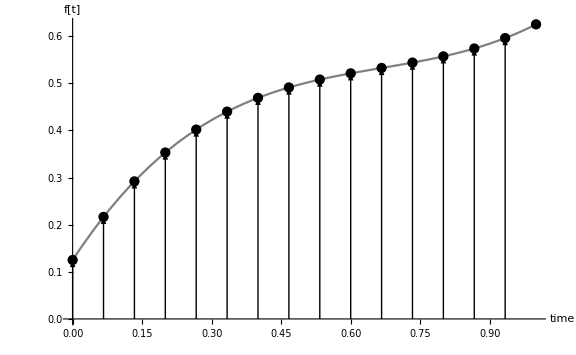
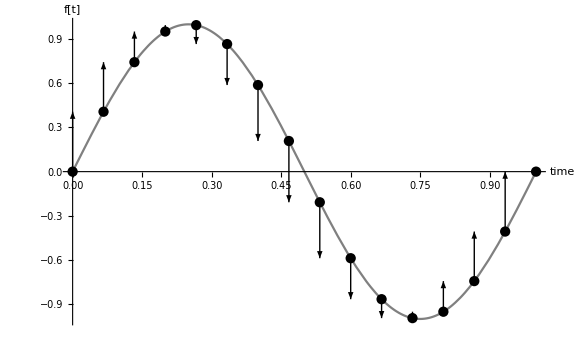

```mathematica
{Show[{
Plot[f[x],{x,0,1},PlotRange->{0,Max[f[t]]},ImageSize->Large,PlotStyle->Gray,AxesLabel->{"time","f[t]"}],
ListPlot[Transpose[{t,f[t]}],PlotStyle->Black],
Graphics[{Arrowheads[Medium],Map[Arrow[{{#,0},{#,f[#]}}]&,Drop[t,-1]]}]
}],
Show[{
Plot[g[x],{x,0,1},ImageSize->Large,PlotStyle->Gray,AxesLabel->{"time","f[t]"}],
ListPlot[Transpose[{t,g[t]}],PlotStyle->Black],
Graphics[Graphics[{Arrowheads[Medium],MapThread[Arrow[{{#1,g[#1]},{#1,g[#2]}}]&,{Drop[t,-1],Drop[t,1]}]}]]
}]}
```

```mathematica
Manipulate[{
Show[{
ParametricPlot[{g[x],f[x]},{x,0,1},PlotRange->{{1.1Min[g[t]],1.1Max[g[t]]},{0,Max[f[t]]}},ImageSize->Large,PlotStyle->Gray,AxesLabel->{"g[x]","f[x]"}],
ListPlot[Transpose[{g[t],f[t]}],PlotStyle->Black],
Graphics[{Arrowheads[Medium],
MapThread[{
Opacity[1],
Arrow[{{g[#1],f[#1]},{g[#2],f[#1]}}],
Arrow[{{g[#1],0},{g[#1],f[#1]}}],
Opacity[.2],
Rectangle[{g[#1],0},{g[#2],f[#1]}]
}&,{Drop[Drop[t,-1],k-n],Drop[Drop[t,1],k-n]}]
}]
}],
Show[
ListPlot[Transpose[{t,Join[{0},Accumulate[dg*f[Drop[t,-1]]]]}],PlotLabel->"Accumulated Area: "<>ToString[N@Total[Drop[dg*f[Drop[t,-1]],k-n]]],ImageSize->Large,PlotStyle->LightGray,AxesLabel->{"time","integral value"}],
ListPlot[{Transpose[{t,Join[{0},Accumulate[dg*f[Drop[t,-1]]]]}][[k+1]]},PlotStyle->Black]
]}
,{k,0,n,1}]
```

## Riemann–Stieltjes Integrals with respect to Brownian Motion

```mathematica
DeleteGeneratedCells[]
```

DeleteGeneratedCells[]

```mathematica
f[x_]:=Exp[x]
n=100;
t = Range[0,n]/n;
Wt=ListInterpolation[First[RandomFunction[WienerProcess[],{0,1,t[[2]]}]["States"]],{{0,1}},InterpolationOrder->1];
dWt = Differences[Wt[t]];
integral =Total[dWt*f[Drop[t,-1]]]
```

3.17505

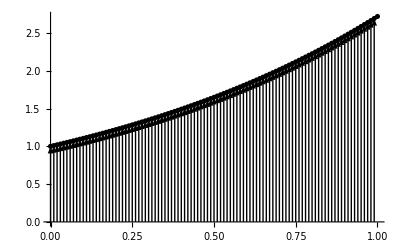

```mathematica
Show[{
Plot[f[x],{x,0,1},PlotRange->{0,Max[f[t]]},PlotStyle->Gray],
ListPlot[Transpose[{t,f[t]}],PlotStyle->Black],
Graphics[Map[Arrow[{{#,0},{#,f[#]}}]&,Drop[t,-1]]]
}]
```

```mathematica
Show[{
Plot[Wt[x],{x,0,1}],
ListPlot[Transpose[{t,Wt[t]}]],
Graphics[Graphics[MapThread[Arrow[{{#1,Wt[#1]},{#1,Wt[#2]}}]&,{Drop[t,-1],Drop[t,1]}]]]
}]
```

```mathematica
Manipulate[{
Show[{
ParametricPlot[{Wt[x],f[x]},{x,0,1},PlotRange->{{1.1Min[Wt[t]],1.1Max[Wt[t]]},{0,Max[f[t]]}},ImageSize->Large,PlotStyle->Gray,AxesLabel->{"W_t[x]","f[x]"}],
ListPlot[Transpose[{Wt[t],f[t]}],PlotStyle->Black],
Graphics[{Arrowheads[Medium],
MapThread[{
Opacity[1],
Arrow[{{Wt[#1],f[#1]},{Wt[#2],f[#1]}}],
Arrow[{{Wt[#1],0},{Wt[#1],f[#1]}}],
Opacity[.2],
Rectangle[{Wt[#1],0},{Wt[#2],f[#1]}]
}&,{Drop[Drop[t,-1],k-n],Drop[Drop[t,1],k-n]}]
}]
}],
Show[
ListPlot[Transpose[{t,Join[{0},Accumulate[dWt*f[Drop[t,-1]]]]}],PlotLabel->"Accumulated Area: "<>ToString[N@Total[Drop[dWt*f[Drop[t,-1]],k-n]]],ImageSize->Large,PlotStyle->LightGray,AxesLabel->{"time","integral value"}],
ListPlot[{Transpose[{t,Join[{0},Accumulate[dWt*f[Drop[t,-1]]]]}][[k+1]]},PlotStyle->Black]
]}
,{k,0,n,1}]
```

#### how can i interpret this as a change of variables?? i think there should be a nice way to see this

```mathematica
Plot[f[ArcSin[x]/(2π)],{x,0,1},PlotRange->All]
```

```mathematica
N@Sin[1]
```